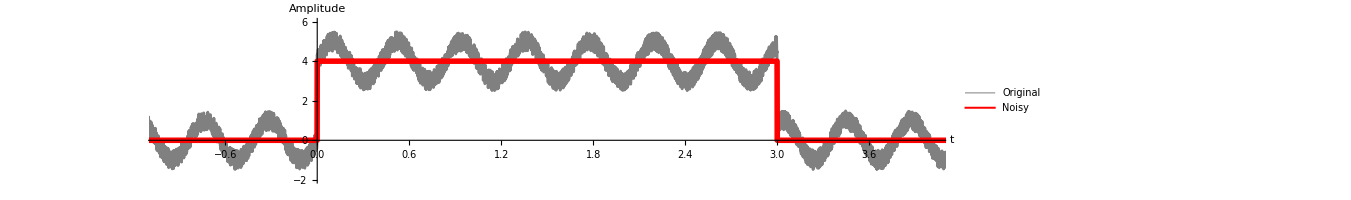

```mathematica
a=4;
t1=0;
t2=3;
c=1;
d=15;
b=0.5;

T=20;
dt=0.001;
tValues=Range[-T/2,T/2,dt];
n=Length[tValues];

vValues=Table[-1/(2 dt)+(k-1)*1/T,{k,n}];

gVals=Table[If[t1<=t<=t2,a,0],{t,tValues}];
xi=RandomReal[{-1,1},n];
uVals=gVals+b*xi+c*Sin[d*tValues];

ListLinePlot[{Transpose[{tValues,uVals}], Transpose[{tValues,gVals}]}, 
AspectRatio->0.2,
PlotLegends->Placed[{"Original", "Noisy"},Right],
 PlotStyle->{{Gray,Thickness[0.002]},{Red, Thickness[0.004]}},
AxesLabel->{"t","Amplitude"},
ImageSize->1000,
PlotRange->{{-1, 4},{-2,6}}
]
```

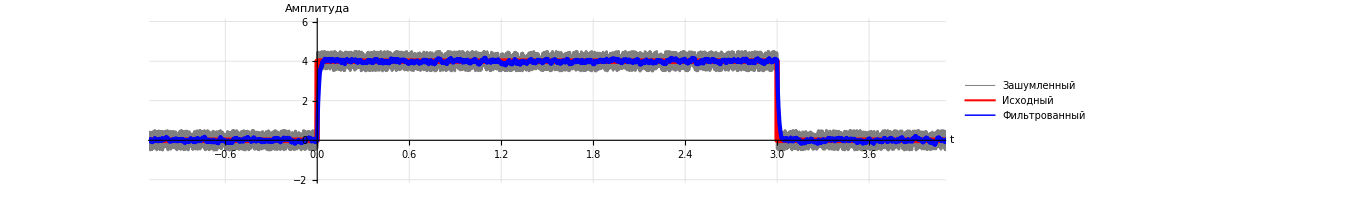

Transpose::nmtx: The first two levels of {{-10.,-9.999,-9.998,-9.997,-9.996,-9.995,-9.994,-9.993,-9.992,-9.991,-9.99,-9.989,-9.988,-9.987,-9.986,-9.985,-9.984,-9.983,-9.982,-9.981,-9.98,-9.979,-9.978,-9.977,-9.976,-9.975,-9.974,-9.973,-9.972,-9.971,-9.97,-9.969,-9.968,-9.967,-9.966,-9.965,-9.964,-9.963,-9.962,-9.961,-9.96,-9.959,-9.958,-9.957,-9.956,-9.955,-9.954,-9.953,-9.952,-9.951,«19951»},Control`LegacySimulationsDump`response3[OutputResponse,{StateSpaceModel,{{{-10.}},{{1.}},{{10.}},{{0.}},Automatic},{{x_1→0.},{u_1→0.}},Automatic,{1.,1.,1.},None},«9»,«1»,{-10.,-9.999,-9.998,«45»,-9.952,-9.951,«19951»},{}]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: {{{-10.,0.769004},{-9.999,0.226151},{-9.998,0.886263},{-9.997,1.14832},{-9.996,0.274597},{-9.995,0.577671},{-9.994,0.905109},{-9.993,0.948459},{-9.992,0.515658},{-9.991,0.762325},{-9.99,1.11706},«29»,{-9.96,0.803918},{-9.959,1.23568},{-9.958,1.20643},{-9.957,0.594413},{-9.956,1.38449},{-9.955,0.821835},{-9.954,1.36555},{-9.953,1.44897},{-9.952,0.859431},{-9.951,0.809024},«19951»},«1»,{}} is not a list of numbers or pairs of numbers.

```mathematica
a=4;
t1=0;
t2=3;
c=0;
d=15;
b=0.5;


T=20;
dt=0.001;
tValues=Range[-T/2,T/2,dt];
n=Length[tValues];

gVals=Table[If[t1<=t<=t2,a,0],{t,tValues}];
xi=RandomReal[{-1,1},n];
uVals=gVals+b*xi+c*Sin[d*tValues];

tau=0.01; (*Постоянная времени фильтра*)
alpha=dt/(tau+dt); (*Коэффициент фильтра*)

(*Цифровая реализация фильтра первого порядка*)
uFiltered=ConstantArray[0,n];
For[i=2,i<=n,i++,uFiltered[[i]]=(1-alpha)*uFiltered[[i-1]]+alpha*uVals[[i]];];

(*Визуализация результатов*)
ListLinePlot[{Transpose[{tValues,uVals}],(*Зашумленный сигнал*)Transpose[{tValues,gVals}],(*Идеальный сигнал*)Transpose[{tValues,uFiltered}] (*Фильтрованный сигнал*)},PlotStyle->{{Gray,Thickness[0.002]},{Red,Thickness[0.004]},{Blue,Thickness[0.003]}},PlotLegends->Placed[{"Зашумленный","Исходный","Фильтрованный"},Right],AspectRatio->0.2,AxesLabel->{"t","Амплитуда"},ImageSize->1000,PlotRange->{{-1,4},{-2,6}},GridLines->Automatic]
```